Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                              < >    Ξ

Edited by Hao Feng

## 6 Learning Rate Schedules and Gradient Descent Variants

Remark:
This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 5, [1], of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation.

In deep learning, the optimization process lies at the heart of training Neural Networks (NNs). Central to this optimization is the notion of the learning rate, a crucial hyperparameter that dictates the step size in the parameter space during optimization. Selecting an appropriate learning rate and its schedule significantly impacts the convergence speed and the final performance of the model. In this chapter, we delve into various learning rate schedules and adaptive algorithms that play pivotal roles in optimizing NNs. By understanding these techniques, practitioners can fine-tune their training processes and achieve better results in their machine-learning endeavors.

The chapter initiates an exploration of learning rate schedules [64-75], which entail predefined strategies for altering the learning rate throughout the training process. Learning rate schedules include step decay, inverse time decay, exponential decay, polynomial decay with warm restart, cyclical learning rate, stochastic gradient descent with warm restarts (cosine decay), exponential decay sine wave learning rate, Hessian-aware learning rate decay, etc., each with its own advantages and drawbacks. Understanding and appropriately implementing these schedules are crucial for achieving optimal convergence without encountering issues such as slow convergence or overshooting the minima.

Transitioning from learning rate schedules, we explore accelerated gradient descent [76-79], a variant of the traditional GD algorithm designed to speed up convergence. Two popular accelerated gradient descent algorithms are SGD with momentum and Nesterov accelerated gradient descent. In both cases, the momentum term helps the optimization algorithm to continue moving in the same direction or accelerate in the relevant direction, even if the gradient changes direction frequently or the surface of the loss function is highly irregular. Both methods help in smoothing out the updates, which is particularly useful when dealing with noisy or high-variance gradients common in SGD. The momentum term helps navigate through the irregularities of the loss surface more effectively, leading to a smoother and often faster path to the minimum. By leveraging past gradients, these methods can speed up convergence, reducing the time and computational resources needed for training. This leads to faster convergence and better overall performance in training NNs and other machine-learning models.

Following the discussion on accelerated gradient descent, we turn our attention to adaptive learning rate algorithms [80-93]. Adaptive learning rate algorithms adaptively adjust the learning rate during training based on past gradients, and other relevant metrics. These algorithms aim to strike a balance between the benefits of using large learning rates for fast convergence and the stability provided by smaller learning rates to prevent overshooting or oscillations. Popular examples include AdaGrad, RMSProp, AdaDelta, Adam, AdaMax, Nadam, and AMSGRAD, each with its own approach to adaptively scale the learning rates for individual model parameters.

Moreover, we explore second-order optimization methods [11,15,25,37]. Second-order optimization methods, such as Newton, Marquardt, and variants like conjugate gradient (Hestenes-Stiefel formula, Polak-Ribiere formula, Fletcher-Reeves formula), and quasi-Newton (rank one correction, DFP, and BFGS), etc., leverage information from the second derivatives of the loss function to guide the optimization process. By incorporating curvature information, these methods can converge faster and more accurately than first-order methods like GD. However, they often come with higher computational costs and memory requirements due to the need to compute and store second-order derivatives or their approximations.

This chapter serves as a continuation of the foundational principles introduced in Chapter 5. Here, we delve into the intricate landscape of learning rate schedules and adaptive algorithms, employing the computational power of Mathematica to elucidate their mechanisms and applications. Divided into two units, this chapter demystifies these fundamental concepts.

The first unit serves as a foundational exploration of learning rate schedules and adaptive optimization algorithms, leveraging the dynamic capabilities of Mathematica to provide intuitive insights. By building optimization algorithms from scratch, the reader gains a deeper understanding of the underlying principles. Through interactive manipulations, readers are guided step by step to comprehend the nuances of various algorithms. From elucidating traditional learning rate schedules such as step decay, inverse time decay, and exponential decay to unraveling sophisticated techniques like accelerated gradient descent and adaptive learning rate algorithms, this unit equips readers with a profound understanding of the mechanisms driving optimization processes. Moreover, Mathematica provides a comprehensive suite of built-in functions and tools for optimization, enabling users to implement, analyze, and visualize a diverse range of optimization problems.

In the second unit, the focus shifts towards practical applications, centering on the optimization of NNs using learning rate schedules and adaptive algorithms within the Mathematica environment. In this unit, we explore the powerful capabilities of Mathematica’s NetTrain function, leveraging a range of optimization methods and suboptions to fine-tune the training process and enhance model performance. NetTrain serves as the cornerstone of NN training within Mathematica, providing a versatile and user-friendly interface for optimizing model parameters. At the heart of NetTrain lies a suite of optimization methods, including “ADAM”, “RMSProp”, “SGD”, and “SignSGD”, each offering unique strategies for navigating the high-dimensional parameter space of NNs. We will not only explore the selection and utilization of these optimization methods but also, we will go into the intricacies of their associated suboptions. These suboptions, including “Momentum”, “Beta1”, “Beta2”, and “Epsilon”, provide users with fine- grained control over the optimization process, allowing for nuanced adjustments to suit the specific requirements of their NN architectures and training objectives.

Furthermore, the “LearningRateSchedule” suboption allows you to specify a learning rate schedule, which can be a fixed learning rate, a schedule that decreases the learning rate over time (such as exponential decay or step decay), or any other custom schedule you define. Through comprehensive demonstrations and hands-on exercises, this unit empowers practitioners to harness the full potential of learning rate schedules and adaptive algorithms in enhancing the performance of NNs.

Together, these units shed light on the nuanced interconnections among learning rate schedules, adaptive algorithms, and NN optimization.

### Understanding Learning Rate Schedules and Adaptive Algorithms with Mathematica

code 6.1 Step Decay

(* The code implements an interactive visualization tool using Mathematica’s Manipulate function to explore the behavior of a step decay learning rate schedule. Users can adjust two parameters, the drop factor (d) and step size (s), via sliders to observe their impact on the learning rate decay. The code defines a step decay function that computes the learning rate based on the initial learning rate, drop factor, step size, and current iteration. Data points representing the learning rate at each iteration are generated and plotted dynamically: *)

```mathematica
Manipulate[
Module[
{data},
stepDecay[initialLearningRate_,dropFactor_,stepSize_,currentIteration_]:=initialLearningRate*dropFactor^Floor[currentIteration/stepSize];

data=Table[{i,stepDecay[initialLearningRate,d,s,i]},{i,0,100}];

ListLinePlot[
data,
PlotRange->All,
PlotLabel->StringForm["Step Decay with d = `` and s = ``",d,s],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{d,0.5,"Drop Factor"},0.1,0.9,0.01},
{{s,10,"Step Size"},1,20,1},
Initialization:>{
initialLearningRate=0.2;
}
]
```

code 6.2 Inverse Time Decay

(* In this Manipulate interface, you can interactively choose different values for the decay rate and observe the corresponding learning rate decay plot. Adjust the decayRate slider to explore how the learning rate changes over iterations according to the inverse time decay formula: *)

```mathematica
Manipulate[
Module[
{data},

inverseTimeDecay[initialLearningRate_,decayRate_,currentIteration_]:=initialLearningRate/(1+decayRate*currentIteration);

data=Table[{i,inverseTimeDecay[initialLearningRate,d,i]},{i,0,100}];

ListLinePlot[
data,
PlotRange->{{0,100},{0.002,1}},
PlotLabel->StringForm["Inverse Time Decay \nInital Rate = `` \nd = ``",initialLearningRate,d],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{initialLearningRate,0.5,"Initial Learning Rate"},0.01,1,0.01},
{{d,0.5,"Decay Rate"},0.01,0.9,0.01}
]
```

code 6.3 Exponential Decay

(* The code uses the standard exponential decay formula, where the learning rate decreases exponentially with the increase in the step. Adjust the sliders for the initial learning rate and decay rate to observe how the learning rate changes over steps according to the standard exponential decay formula: *)

```mathematica
Manipulate[
Module[
{data},
exponentialDecay[initialLearningRate_,decayRate_,currentIteration_]:=initialLearningRate*Exp[-decayRate*currentIteration];

data=Table[{i,exponentialDecay[initialLearningRate,decayRate,i]},{i,0,100}];

ListLinePlot[
data,
PlotRange->{{0,100},{0.002,1}},
PlotLabel->StringForm["Exponetial Decay\nInitial Rate = ``,\nDecay Rate=``",initialLearningRate,decayRate],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{initialLearningRate,0.5,"Initial Learning Rate"},0.01,1,0.01},
{{decayRate,0.5,"Decay Rate"},0.1,1,0.01}
]
```

code 6.4 Exponential Decay and Inverse Time Decay

(* The code defines both exponential decay and inverse time decay functions and generates data for both methods. It then plots the learning rates over steps for comparison. Adjust the sliders for the initial learning rate, decay rate, and decay steps to observe how the learning rates evolve using both decay methods: *)

```mathematica
Manipulate[
Module[
{dataExp,dataInvTime},

exponentialDecay[initialLearningRate_,decayRate_,currentStep_]:=initialLearningRate*Exp[-decayRate*currentStep];
inverseTimeDecay[initialLearningRate_,decayRate_,currentIteration_]:=initialLearningRate/(1+decayRate*currentIteration);
dataExp=Table[{i,exponentialDecay[initialLearningRate,decayRate,i]},{i,0,100}];
dataInvTime=Table[{i,inverseTimeDecay[initialLearningRate,decayRate,i]},{i,0,100}];

ListLinePlot[
{dataExp,dataInvTime},
PlotRange->{{0,100},{0.002,1}},
PlotLabel->"Exponential Decay and Inverse Time Decay",
PlotLegends->Placed[{"Exponential Decay","Inverse Time Decay"},{0.7,0.78}],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{initialLearningRate,0.7,"Initial Learning Rate"},0.01,1,0.01},
{{decayRate,0.1,"Decay Rate"},0.01,0.9,0.001}
]
```

code 6.5 Polynomial Decay

(* The code aims to create an interactive visualization tool for exploring polynomial decay in learning rate dynamics. Utilizing Mathematica’s Manipulate function, users can dynamically adjust parameters such as the initial learning rate, power of the polynomial decay function, and total iterations via sliders. Within the module, a polynomial decay function is defined to compute the learning rate at each iteration based on the specified parameters. Data points representing the learning rate over iterations are generated and plotted using ListLinePlot, with the plot displaying the decay curve: *)

```mathematica
Manipulate[
Module[
{data},
polynomialDecay[initialLearningRate_,power_,totalIterations_,currentIteration_]:=initialLearningRate*(1-currentIteration/totalIterations)^power;

data=Table[{i,polynomialDecay[initialLearningRate,power,totalIterations,i]},{i,0,totalIterations}];

ListLinePlot[
data,
PlotRange->{{0,2000},{0.002,1}},
PlotLabel->StringForm["Polynomial Decay\nInitial Rate=``,Power=``,Total Iterations=``",initialLearningRate,power,totalIterations],
AxesLabel->{"Iterations","Learning Rate"},
ImageSize->300
]
],
{{initialLearningRate,0.7,"Initial Learning Rate"},0.01,1,0.01},
{{power,0.9,"Power"},0.1,2,0.1},
{{totalIterations,1500,"Total Iterations"},100,2000,100},
Initialization:>{(*Set parameters*)}
]
```

code 6.6 Polynomial Decay with Warm Restarts

(* The code aims to analyze and visualize polynomial decay with warm restarts, a technique often employed in training NN. It defines a function, polynomialDecayWithRestart, within a module to simulate learning rate decay with periodic resets to prevent convergence to suboptimal solutions. Parameters such as the initial learning rate, powers representing different decay rates, total iterations, and warm restart fractions are defined to allow for customizable exploration of decay strategies. Data lists are generated for various decay powers using nested table commands, and these are plotted using ListLinePlot. The resulting plot displays the learning rate strategies, with each curve representing a different decay rate: *)

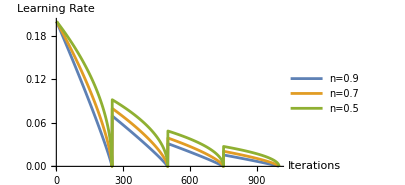

```mathematica
polynomialDecayWithRestart[initialLearningRate_,power_,totalEpochs_,restartFractions_,currentIterations_]:=Module[
{restartPoints,currentEpoch,currentLearningRate,currentIteration,totalEpoch},
restartPoints=Round[restartFractions*totalEpochs];

Piecewise[
{
{{currentLearningRate,totalEpoch}={initialLearningRate,restartPoints[[1]]};,
restartPoints[[1]]>=currentIterations>=1},
{{currentLearningRate,totalEpoch}={initialLearningRate*0.65,restartPoints[[2]]};,
restartPoints[[2]]>=currentIterations>=restartPoints[[1]]+1},
{{currentLearningRate,totalEpoch}={initialLearningRate*0.65^2,restartPoints[[3]]};,
restartPoints[[3]]>=currentIterations>=restartPoints[[2]]+1},
{{currentLearningRate,totalEpoch}={initialLearningRate*0.65^3,totalEpochs};,
totalEpochs>=currentIterations>=restartPoints[[3]]+1}
}
];
currentLearningRate*(1-currentIterations/totalEpoch)^power
];

initialLearningRate=0.2;
powers={0.9,0.7,0.5};
totalIterations=1000;
restartFractions={0.25,0.5,0.75};

dataLists=Table[
Table[
{i,polynomialDecayWithRestart[initialLearningRate,power,totalIterations,restartFractions,i]},
{i,0,totalIterations}
],
{power,powers}
];

ListLinePlot[
dataLists,
PlotRange->All,
AxesLabel->{"Iterations","Learning Rate"},
PlotLegends->Placed[{"n=0.9","n=0.7","n=0.5"},{0.85,0.78}],
ImageSize->300
]
```

code 6.7 Cyclical Learning Rates

(* Cyclical Learning Rates (CLR) proves particularly valuable in overcoming challenges associated with saddle points in the loss landscape. The code presented below creates an interactive environment for exploring the impact of different parameters on the cyclical learning rate schedule. Key Parameters adjusted via Manipulate are base learning rate, the initial learning rate at the start of each cycle, max learning rate, the peak learning rate reached during a cycle, half cycle length, a parameter controlling how quickly the learning rate increases and decreases, and total iterations, the number of iterations to visualize. As users manipulate these parameters using sliders, the code dynamically recalculates and visualizes the corresponding cyclical learning rate schedule. The resulting plot provides insights into how changes in the learning rate parameters impact the training process, offering an intuitive understanding of CLR’s adaptability and efficiency: *)

```mathematica
triangularLR[epoch_,stepsize_,baseLR_,maxLR_]:=Module[
{cycle,x,lr},
cycle=Floor[1+epoch/(2*stepsize)];
x=Abs[epoch/stepsize-2*cycle+1];
lr=baseLR+(maxLR-baseLR)*Max[0,(1-x)];
lr 
]

Manipulate[
Module[
{epochs,LearningRates},
epochs=Range[1,totalIterations];
LearningRates=triangularLR[#,stepsize,baseLR,maxLR]&/@epochs;

ListLinePlot[
Transpose[{epochs,LearningRates}],
PlotLabel->"Cyclical Learning Rate Schedule",
PlotRange->{{1,200},{0.005,0.4}},
Joined->True,
Mesh->All,
MeshStyle->Directive[PointSize[0.01],Purple],
ImageSize->300
]
],
{{baseLR,0.1,"Base Learning Rate"},0.1,0.2,0.0001,Appearance->"Labeled"},{{maxLR,0.2,"Max Learning Rate"},0.2,0.3,0.001,Appearance->"Labeled"},{{stepsize,5,"Half Cycle Length"},5,10,1,Appearance->"Labeled"},{{totaliterations,100,"Total Epochs"},10,200,20,Appearance->"Labeled"}
]
```

code 6.8 Cosine Annealing Learning Rate Scheduler

(* The code implements a cosine annealing learning rate scheduler within a Manipulate environment, allowing users to interactively explore and visualize the learning rate schedule. It defines a function, CosineAnnealingLR, to compute learning rates based on parameters such as the minimum and maximum learning rates, total iterations in a cycle, and the current iteration number. The code generates learning rates over multiple cycles using the cosine annealing method and plots the learning rate schedule using ListLinePlot. Users can adjust hyperparameters such as the minimum and maximum learning rates, total iterations in a cycle, and the number of cycles through sliders to observe the corresponding changes in the learning rate schedule: *)

```mathematica
Manipulate[
CosineAnnealingLR[minLR,maxLR,Ti,Tcur_]:=minLR+0.5(maxLR-minLR)(1+Cos[(Tcur/Ti)π]);
cycles=Flatten[Table[Range[0,Ti],numCycles]];
learningRates=CosineAnnealingLR[minLR,maxLR,Ti,#]&/@cycles;
epochs=Range[1,Length[cycles]];
data=Transpose[{epochs,learningRates}];

ListLinePlot[
data,
PlotRange->{{1,1000},{0.005,0.15}},
AxesLabel->{"Iterations","Learning Rate"},
PlotLabel->"Cosine Annealing Learning Rate Schedule",
Joined->True,
ImageSize->300
],
{{minLR,0.02,"Minimum LR"},0,0.1,0.0001,Appearance->"Labeled"},{{maxLR,0.08,"Maximum LR"},0,0.1,0.0001,Appearance->"Labeled"},{{Ti,50,"Total Iterations in a Cycle"},10,100,1,Appearance->"Labeled"},{{numCycles,4,"Total Cycles"},1,10,1,Appearance->"Labeled"}
]
```

code 6.9 Stochastic Gradient Descent with Restarts

(* The code constructs a learning rate schedule based on the stochastic gradient descent with restarts (SGDR) method utilizing cosine annealing. It initializes parameters such as the multiplier factor for cycle length, the initial cycle length, and the number of cycles. Subsequently, it calculates the cycle lengths and computes learning rates for each iteration within each cycle using the SGDRCosineLR function, which implements the cosine annealing formula. The resulting learning rate schedule is then visualized using ListLinePlot, displaying epochs against corresponding learning rates: *)

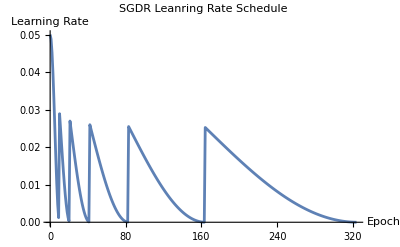

```mathematica
Tmult=2;
T[0]=10;
numofcycles=4;

Ti=Table[T[i+1]=T[i]*Tmult;T[i+1],{i,0,numofcycles}];
TiValues=Flatten[PrependTo[Ti,{1,T[0]}]];

nmin=0.0;
nmax=0.05;
SGDRCosineLR[nmin_,nmax_,Tcur_,Ti_]:=nmin+1/2(nmax-nmin)(1+Cos[Tcur/Ti π])

lrValues=Flatten[Table[
Table[
SGDRCosineLR[nmin,nmax,t,TiValues[[j+1]]],
{t,TiValues[[j]]-1,TiValues[[j+1]]-1}
],
{j,1,Length[TiValues]-1}
]];

epochs=Range[0,Length[lrValues]-1];

ListLinePlot[
Transpose[{epochs,lrValues}],
AxesLabel->{"Epoch","Learning Rate"},
PlotLabel->"SGDR Leanring Rate Schedule"
]
```

code 6.10 Exponential Decay Sine Wave Learning Rate

(* The code implements a Manipulate interface in Mathematica, facilitating interactive exploration of a custom learning rate schedule. The schedule is defined by a function combining exponential decay and sine wave oscillation components. Users can adjust parameters such as the initial learning rate, decay rate, total iterations, oscillation parameter, and number of batches per epoch. These parameters influence the shape and behavior of the learning rate schedule, impacting the optimization process. The interface dynamically updates a plot showcasing the learning rate schedule, enabling users to visualize how changes in parameters affect the rate at which the algorithm adjusts its weights during training: *

```mathematica
Manipulate[
Module[
{lrFunction,initialRate,decayRate,totalIterations,oscillationParam,batchesPerEpoch},
lrFunction[t_,initialRate_,decayRate_,totalIterations_,oscillationParam_,batchesPerEpoch_]:=initialRate Exp[-(decayRate t)/totalIterations](Sin[(oscillationParam t)/(2π batchesPerEpoch)]+Exp[-(decayRate t)/totalIterations]+0.5);

initialRate=initialRate0;
decayRate=decayRate0;
totalIterations=totalIterations0;
oscillationParam=oscillationParam0;
batchesPerEpoch=batchesPerEpoch0;

Plot[
lrFunction[t,initialRate,decayRate,totalIterations,oscillationParam,batchesPerEpoch],
{t,0,totalIterations},
AxesLabel->{"Iteration","Learning Rate"},
PlotRange->{Automatic,{0.005,2.5}},
ImageSize->300
]
],
{{initialRate0,0.59,"Initial learning rate (α₀)"},0,1,0.01},{{decayRate0,0.6,"Decay rate (ρ)"},0,1,0.01},{{totalIterations0,50000,"Total iterations (T)"},100,1000000,1000},{{oscillationParam0,0.05,"Oscillation parameter (τ)"},0,1,0.01},{{batchesPerEpoch0,10,"Number of batches per epoch (b)"},1,100,1},ControlPlacement->Left
]
```

code 6.11 Hessian-Aware Learning Rate Schedule

(* The code creates a Manipulate interface that allows users to visualize and interact with the Hessian-Aware Learning Rate schedule based on specific parameters. The code defines a piecewise learning rate function, allowing for different learning rates to be applied in various epochs of the training process. Users can adjust parameters such as the initial learning rate, decay factor, starting epoch for decay, ending epoch for decay, and total number of epochs. The interface dynamically updates the plotted learning rate decay curve based on the chosen parameter values, providing users with insights into how changes in these parameters affect the learning rate schedule during training: *)

```mathematica
Manipulate[
Module[
{lr,decayFunc,data},
decayFunc[t_]:=decayFunc[t-1]*decayFactor^(1/(endEpoch-startEpoch));
lr[t_,initialLR_,decayFactor_,startEpoch_,endEpoch_,totalEpochs_]:=Piecewise[
{
{initialLR,1<=t<startEpoch},
{decayFunc[t],startEpoch<t<=endEpoch},
{decayFactor*initialLR,endEpoch<t<=totalEpochs}
}
];

decayFunc[startEpoch]=initialLR;

data=Table[{t,lr[t,initialLR,decayFactor,startEpoch,endEpoch,totalEpochs]},{t,1,totalEpochs}];
ListLinePlot[
data,
PlotRange->{{1,1000},{0,1}},
AxesLabel->{"Epoch","Learning Rate"},
PlotRange->All,
GridLines->{{startEpoch,endEpoch},{initialLR,decayFactor*initialLR}},
Epilog->{
Text["initialLR",{startEpoch,initialLR},{3,2}],
Text["decayFactor*initialLR",{endEpoch,decayFactor*initialLR},{-1,-1}]
}
]
],
{{initialLR,0.7,"Initial learning rate (initialLR)"},0,1,0.01},{{decayFactor,0.28,"Decay factor (decayFactor)"},0,1,0.01},{{startEpoch,350,"Starting epoch for decay (startEpoch)"},1,totalEpochs-1,1},{{endEpoch,480,"Ending epoch for decay (endEpoch)"},startEpoch+1,totalEpochs,1},{{totalEpochs,900,"Total number of epochs (totalEpochs)"},10,1000,10},ControlPlacement->Left
]
```

code 6.12 Gradient Descent with Momentum (1D)

(* The code showcases the implementation and visualization of gradient descent with momentum for optimizing the function f(x)=x^2*sin(x). The code defines the function and its derivative, then employs a gradient descent algorithm with momentum to iteratively update the value of x towards the minimum of the function. Through interactive controls, users can adjust parameters such as the initial point, number of steps, learning rate, and momentum parameter, allowing them to observe how different settings affect the optimization process, convergence speed, and trajectory: *)

```mathematica
targetFunction[x_]:=x^2*Sin[x]

functionDerivative[x_]:=x^2 Cos[x]+2 x Sin[x]

gradientDescentWithMomentum[func_,funcDerivative_,initialPoint_,learningRate_,momentumParameter_,iterations_]:=Module[
{x=initialPoint,v=0,path={initialPoint}},
For[
i=1,
i<=iterations,
i++,

v=momentumParameter*v-learningRate*funcDerivative[x];
x=x+v;
AppendTo[path,x];
];
Return[path];
]

Manipulate[
path=gradientDescentWithMomentum[targetFunction,functionDerivative,initialPoint,learningRate,momentumParameter,steps];

Plot[
targetFunction[x],
{x,-5,9},
Epilog->{Purple,PointSize[0.02],Point[Thread[{path,targetFunction/@path}]]},
PlotLabel->"Gradient Descent with Momentum",
AxesLabel->{"x","f(x)"},
ImageSize->300
],
{{initialPoint,-5,"Initial Point"},-6,6,Appearance->"Labeled"},{{steps,1,"Steps"},1,50,1,Appearance->"Labeled"},{{learningRate,0.01,"Learning Rate"},0.001,0.1,Appearance->"Labeled"},{{momentumParameter,0.95,"Momentum Parameter"},0.1,0.99,Appearance->"Labeled"}
]
```

code 6.13 Gradient Descent with Momentum (2D)

(* The code defines a target function f(x,y)=x^2*sin(x)+y^2*sin(y) and its gradient, and implements gradient descent with momentum for optimization. It allows interactive manipulation of parameters such as the initial point, number of iterations, learning rate, and momentum parameter. The optimization process is visualized through a contour plot of the target function overlaid with the optimization path and step direction arrows. The primary goal is to demonstrate the convergence of the gradient descent algorithm with momentum towards the minimum point of the target function, providing an intuitive understanding of the optimization process: *)

```mathematica
targetFunction[x_,y_]=x^2*Sin[x]+y^2*Sin[y];
functionGradient[x_,y_]=Grad[targetFunction[x,y],{x,y}];

gradientDescentWithMomentum[func_,grad_,initialPoint_,learningRate_,momentumParameter_,iterations_]:=Module[
{x=initialPoint,v={0,0},path={initialPoint}},
For[
i=1,
i<=iterations,
i++,

v=momentumParameter*v-learningRate*grad@@x;
x=x+v;
AppendTo[path,x];
];
Return[path];
];

Manipulate[
Module[
{path,minPoint},
path=gradientDescentWithMomentum[targetFunction,functionGradient,initialPoint,learningRate,momentumParameter,iterations];
stepArrows=Arrow/@Partition[path,2,1];

Show[
ContourPlot[
targetFunction[x,y],
{x,-10,10},
{y,-10,10},
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->300,
PlotLegends->Automatic,
PlotLabel->"Gradient Descent with Momentum",
AspectRatio->Automatic
],
Graphics[
{
Blue,
PointSize[0.015],
Point[path],
Purple,
stepArrows
}
]
]
],
{{initialPoint,{-5.3,7.6},"Initial Point"},{-10,-10},{10,10},Appearance->"Labeled"},{{iterations,1,"Iterations"},1,100,1,Appearance->"Labeled"},{{learningRate,0.001,"Learning Rate"},0.001,0.01,Appearance->"Labeled"},{{momentumParameter,0.99,"Momentum Parameter"},0.1,0.99,Appearance->"Labeled"},TrackedSymbols:>{initialPoint,iterations,learningRate,momentumParameter}
]
```

code 6.14 Nesterov Accelerated Gradient Descent

(* The code implements an interactive visualization of the Nesterov Accelerated Gradient Descent optimization algorithm. It defines an objective function f(x1,x2)=sin(x1)+cos(x2) and its gradient, allowing users to adjust parameters such as learning rate, momentum, number of iterations, and initial guess through interactive controls. Within a module, the Nesterov Accelerated Gradient Descent algorithm is executed, updating parameters iteratively and storing the trajectory of parameter updates. The visualization consists of a contour plot of the objective function overlaid with the trajectory of parameter updates, enabling users to observe how the optimization algorithm progresses towards the function’s minimum, with arrows indicating the direction of parameter updates at each iteration: *)

```mathematica
Manipulate[
Module[
{f,gradient,learningRate,momentum,numIterations,initialGuess,x,v,trajectory},
f[x1_,x2_]=Sin[x1]+Cos[x2];
gradient[x1_,x2_]={D[f[x1,x2],x1],D[f[x1,x2],x2]};

learningRate=lr;
momentum=m;
numIterations=n;
initialGuess={x0,y0};

x=initialGuess;
v={0,0};
trajectory={x};

Do[
lookaheadParams=x+momentum*v;
grad=gradient@@lookaheadParams;

v=momentum*v-learningRate*grad;
x=x+v;
AppendTo[trajectory,x],
{i,numIterations}
];
{
Plot3D[
f[x1,x2],
{x1,-5,5},
{x2,-5,5},
PlotRange->All,
Mesh->None,
ImageSize->300,
ColorFunction->"BlueGreenYellow",
PlotLabel->"Nesterov Accelerated Gradient Descent Trajectory"],
ContourPlot[
f[x1,x2],
{x1,-5,5},
{x2,-5,5},
PlotRange->All,
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
ImageSize->300,
PlotLegends->Automatic,
Epilog->{
Red,
PointSize[Medium],
Point[trajectory],
Blue,
Arrowheads[0.02],
Table[
Arrow[{trajectory[[i]],trajectory[[i+1]]}],
{i,Length[trajectory]-1}
]
},
FrameLabel->{"x1","x2"},
PlotLabel->"Nesterov Accelerated Gradient Descent Trajectory"
]
}
],
{{lr,0.1,"Learning Rate"},0.01,1,0.01},{{m,0.9,"Momentum"},0,1,0.01},{{n,1,"Number of Iterations"},1,50,1},{{x0,1.5,"Initial x1"},-4,4,0.1},{{y0,-0.5,"Initial x2"},-4,4,0.1}
]
```

code 6.15 AdaGrad Optimization

(* The code implements AdaGrad optimization to optimize the objective function sin(x)+cos(y). It defines functions to compute the gradient of the objective function, as well as the AdaGrad optimization procedure itself. Through a Manipulate interface, users can interactively set initial variable values, learning rate, epsilon, and the maximum number of iterations, while visualizing the trajectory of the optimization process on a contour plot of the objective function: *)